Implementation  of  iterated  von  Neumann  extractor
Rok Zitko, 8 Nov 2024
Reference: Yuval Peres, Iterating von Neumann’s prodecure for extracting random bits,
The Annals of Statistics 20, 590 (1992)

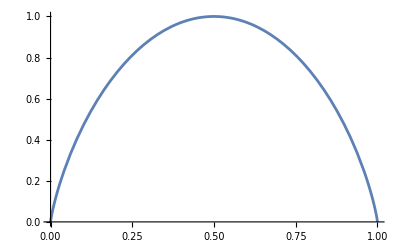

```mathematica
h[p_]:=-p Log[2,p]-(1-p)Log[2,1-p];
Plot[h[p],{p,0,1}]
```

```mathematica
p=0.2;
n=1000000;
h[p]
l=RandomVariate[BernoulliDistribution[p],n];
Mean[l]//N
```

0.721928

0.200337

```mathematica
Take[l,10]
```

{0,0,1,1,0,0,1,0,0,0}

```mathematica
kindexes[l_]:=Flatten[Position[Equal@@@Partition[l,2],False]]
iindexes[l_]:=Flatten[Position[Equal@@@Partition[l,2],True]]
```

```mathematica
k0=kindexes[l];
i0=iindexes[l];
Length@Union[i0,k0]==n/2
```

True

```mathematica
xor[a_,b_]:=Mod[a+b,2];
{xor[0,0],xor[0,1],xor[1,0],xor[1,1]}=={0,1,1,0}
```

True

```mathematica
ClearAll[Ψ];
Ψ[1,l_]:=l[[2kindexes[l]]];
```

```mathematica
ulist[l_]:=xor@@@Partition[l,2];
vlist[l_]:=l[[2iindexes[l]]];
```

```mathematica
Length[Ψ[1,l]]+Length[ulist[l]]+Length[vlist[l]]==n
```

True

```mathematica
l1=Ψ[1,l];
Length[l1]
Mean[l1]//N
```

160339

0.499804

```mathematica
Ψ[ν_,l_]:=Ψ[ν,l]=Join[Ψ[1,l],Ψ[ν-1,ulist[l]],Ψ[ν-1,vlist[l]]];
```

```mathematica
l2=Ψ[2,l];
Length[l2]
Mean[l2]//N
```

288007

0.499651

```mathematica
tab=Table[ll=Ψ[ν,l];{ν,Length[ll],Mean[ll]//N},{ν,1,20}];
TableForm[tab]
```

1 | 160339 | 0.499804
2 | 288007 | 0.499651
3 | 387652 | 0.49983
4 | 465978 | 0.49941
5 | 525947 | 0.499448
6 | 572672 | 0.499309
7 | 608380 | 0.499239
8 | 635683 | 0.499261
9 | 656430 | 0.499455
10 | 672607 | 0.49944
11 | 684609 | 0.499603
12 | 693665 | 0.499552
13 | 700426 | 0.499547
14 | 705124 | 0.499583
15 | 708137 | 0.49958
16 | 709652 | 0.499567
17 | 710187 | 0.499564
18 | 710307 | 0.499574
19 | 710318 | 0.499575
20 | 710318 | 0.499575